# Computational Analysis of the Time Dependent Schroedinger Equation

By: Andrew DeBenedictis, Anna Phillips, and Jen Radoff

## Introduction

For this project, we examined solutions to the time dependent schrodinger equation using two schemes: a simple finite difference scheme and the Crank-Nicolson scheme. Since the finite difference scheme failed to preserve normalization in the simple case of a free particle, we only present the Crank-Nicolson scheme for the various potentials. Our code is capable of doing those runs, though.

## Importing Python-generated data

```mathematica
NotebookDirectory[]
```

/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 6/GradStudentsRock_TDSE/

```mathematica
path=NotebookDirectory[];
cases={"freeParticle","squareWell","harmonicOscillator","triangle","kronigPenney","imagPotential","complexPotential","barrier1","barrier2","barrier3","squareWellwithEigenState","harmonicOscillatorEigenState"};
scheme={"_SFD","_CN"};
numberType={"Real","Imag"};
periodicType={"periodic","nonPeriodic"};
eigenState = {"eValues","eVectors"};
```

## Free Particle

Let’s look at the eigenvalues and eigenvectors to start out since these are scheme-independent:

```mathematica
Clear[freeEVectorsRe,freeEVectorsIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=1;
 schemeChoice=1;
freeEValues=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦1⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
Do[
Evaluate[Symbol["freeEVectors"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>"_"<>eigenState⟦2⟧<>".csv","CSV"];,
{i,2}];
freeEVectors=Sqrt[freeEVectorsRe^2+freeEVectorsIm^2];
];
```

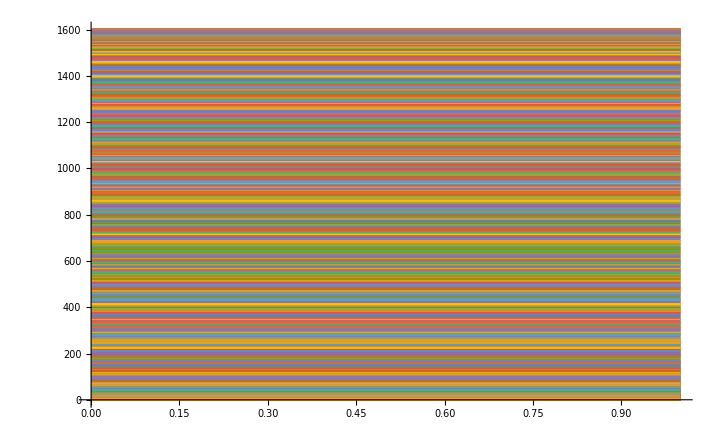

```mathematica
Plot[freeEValues,{x,0,1}]
```

Those are densely packed, as they should be!

```mathematica
Manipulate[ListPlot[freeEVectors⟦All,i⟧,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{i,1,Length[freeEVectors⟦All,1⟧],1}]
```

These look wonky, but that seems possible for the free particle--we should be able to create oscillatory waves at nearly any frequency that would be eigenstates. So it’s probably that the system is underdetermined, but nonetheless, our result appears plausible.

### Scheme 1: Simple Finite DiffereCNe (SFD)

this imports in form {rows, columns} equal to {time, position}

```mathematica
Clear[freeRe,freeIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=1;
 schemeChoice=1;
Do[
Evaluate[Symbol["free"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
free=Sqrt[freeRe^2+freeIm^2];
];
```

```mathematica
Manipulate[ListPlot[{free⟦t,All⟧,freeRe⟦t,All⟧,freeIm⟦t,All⟧},PlotRange->{-.7,.7},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[freeRe⟦All,1⟧],1}]
```

Well, that seems to not work well. The wave decoheres quickly and flattens.

### Scheme 2: Crank-Nicolson (CN)

This should be the more stable scheme. For the rest of the cases, we will implement this scheme.

this imports in form {rows, columns} equal to {time, position}

```mathematica
Clear[freeCNRe,freeCNIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=1;
 schemeChoice=2;
Do[
Evaluate[Symbol["freeCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
freeCN=Sqrt[freeCNRe^2+freeCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{freeCN⟦t,All⟧,freeCNRe⟦t,All⟧,freeCNIm⟦t,All⟧},PlotRange->{-.7,.7},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[freeCNRe⟦All,1⟧],1}]
```

The wave still does decohere, but it takes much longer. We also see it spread out, but doesn’t flatten as before.

#### Let’s compare the two schemes directly

```mathematica
Manipulate[ListPlot[{free⟦t,All⟧,freeCN⟦t,All⟧},PlotRange->{0,.7},Joined->True,PlotLegends->{"Simple finite difference", "Crank-Nicolson"},DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[freeCNRe⟦All,1⟧],1}]
```

The flattening effect is quite significant.

#### and check normalization

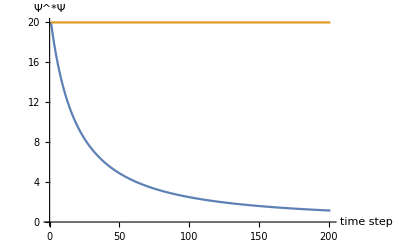

```mathematica
ListPlot[{Total[free^2,{2}],Total[freeCN^2,{2}]},Joined->True,AxesLabel->{"time step","Ψ^*Ψ"}]
```

Scheme 2 doesn’t lose normalization!

### Scheme 2 with non-Periodic boundary conditions

We can see what happens when we effectively put our free particle in a box by fixing the edges.

```mathematica
Clear[freeNonPeriodicCNRe,freeNonPeriodicCNIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["freeNonPeriodicCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
freeNonPeriodicCN=Sqrt[freeNonPeriodicCNRe^2+freeNonPeriodicCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{freeNonPeriodicCN⟦t,All⟧,freeNonPeriodicCNRe⟦t,All⟧,freeNonPeriodicCNIm⟦t,All⟧},PlotRange->{-.7,.7},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[freeNonPeriodicCNRe⟦All,1⟧],1}]
```

SPLAT!

Using the joined option seems to hide the fact that the very end data point does connect to zero.

## Square Well

We’ll look at two versions of the square well: one with our gaussian wave packet, and another with an actual eigenstate (cos(nx/L)).

With a wave packet.

```mathematica
Clear[squareCNRe,squareCNIm,squareCN,squarePotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=2;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["squareCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
squarePotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
squareCN=Sqrt[squareCNRe^2+squareCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{squareCN⟦t,All⟧,squareCNRe⟦t,All⟧,squareCNIm⟦t,All⟧,squarePotential},PlotRange->{-.7,.7},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,Joined->True],{t,1,Length[squareCNRe⟦All,1⟧],1}]
```

That looks exactly like what we’d expect! Let’s look at our eigenvectors.

```mathematica
Clear[squareEVectorsRe,squareEVectorsIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=2;
periodicChoice=2;
 schemeChoice=2;
squareEValues=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦1⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
Do[
Evaluate[Symbol["squareEVectors"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>"_"<>eigenState⟦2⟧<>".csv","CSV"];,
{i,2}];
squareEVectors=Sqrt[squareEVectorsRe^2+squareEVectorsIm^2];
];
```

```mathematica
Manipulate[ListPlot[{squareEVectors⟦All,i⟧,squareEVectorsRe⟦All,i⟧,squareEVectorsIm⟦All,i⟧},Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,PlotRange->Full,PlotLegends->{"|V|", "Re[V]", "Im[V]"}],{i,1,Length[squareEVectors⟦All,1⟧],1}]
```

171 is the ground state, 172 is the first excited state. Most of the sensible-looking states appear in that range. Note that the eigenvectors are real--we expect that.

So there seem to be some very odd states in here (likely coming from the fact that our particle in a “box” is only set to be a semi-infinite well (1000 units high). Once the energy gets large, it makes sense that the particle could be behind the walls.

Let’s look at the first few energy eigenstates.

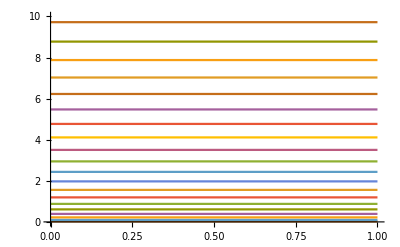

```mathematica
Plot[squareEValues,{x,0,1},PlotRange->{{0,1},{0,10}}]
```

As we’d expect, we see the separation between the eigenstates increasing.

#### With an initial cosine wave.

Since we can’t seem to calculate an eigenvector, let’s input it manually.

```mathematica
Clear[squareCosCNRe,squareCosCNIm,squareCosCN,squareCosPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=11;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["squareCosCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
squareCosPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
squareCosCN=Sqrt[squareCosCNRe^2+squareCosCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{squareCosCN⟦t,All⟧,squareCosCNRe⟦t,All⟧,squareCosCNIm⟦t,All⟧,squareCosPotential},PlotRange->{-.5,1.2},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,Joined->True],{t,1,Length[squareCosCNRe⟦All,1⟧],1}]
```

We can see that this is pretty stable, though it does slowly destabalize over time (which is what we’d expect). s

## Harmonic Oscillator

With a wave packet

```mathematica
Clear[hoCNRe,hoCNIm,hoCN,hoPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=3;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["hoCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
hoPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
hoCN=Sqrt[hoCNRe^2+hoCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{hoCN⟦t,All⟧,hoCNRe⟦t,All⟧,hoCNIm⟦t,All⟧,hoPotential/200},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,DataRange->{-20,20}, AxesOrigin->{-20,0},Joined->True],{t,1,Length[hoCNRe⟦All,1⟧],1}]
```

```mathematica
Clear[hoEVectorsRe,hoEVectorsIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=3;
periodicChoice=2;
 schemeChoice=2;
hoEValues=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦1⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
Do[
Evaluate[Symbol["hoEVectors"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>"_"<>eigenState⟦2⟧<>".csv","CSV"];,
{i,2}];
hoEVectors=Sqrt[hoEVectorsRe^2+hoEVectorsIm^2];
];
```

```mathematica
Manipulate[ListPlot[{hoEVectors⟦All,i⟧,hoEVectorsRe⟦All,i⟧,hoEVectorsIm⟦All,i⟧},Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,PlotRange->{{-20,20},{-.4,.4}}],{i,1,Length[hoEVectors⟦All,1⟧],1}]
```

53 is the ground state, then they are in a sensible order for a while.

We see some states that look like Airy functions, which is vaguely sensible, and then bunch of states that look like what we expect starting at 53.

#### With an initial eigenstate

We can start our particle off in an eigenstate.

```mathematica
Clear[hoEigCNRe,hoEigCNIm,hoEigCN,hoEigPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=12;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["hoEigCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
hoEigPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
hoEigCN=Sqrt[hoEigCNRe^2+hoEigCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{hoEigCN⟦t,All⟧,hoEigCNRe⟦t,All⟧,hoEigCNIm⟦t,All⟧,hoEigPotential/200},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,DataRange->{-20,20}, AxesOrigin->{-20,0},Joined->True],{t,1,Length[hoEigCNRe⟦All,1⟧],1}]
```

This seems to alternate real vs imaginary parts, but |Ψ|^2 stays about constant.

## Triangle

Here is our triangle potential.

```mathematica
Clear[triCNRe,triCNIm,triCN,triPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=4;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["triCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
triPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
triCN=Sqrt[triCNRe^2+triCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{triCN⟦t,All⟧,triCNRe⟦t,All⟧,triCNIm⟦t,All⟧,triPotential/50},PlotRange->{-.7,.7},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[triCNRe⟦All,1⟧],1}]
```

Let’s look at the eigenvectors.

```mathematica
Clear[triEVectorsRe,triEVectorsIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=4;
periodicChoice=2;
 schemeChoice=2;
triEValues=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦1⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
Do[
Evaluate[Symbol["triEVectors"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>"_"<>eigenState⟦2⟧<>".csv","CSV"];,
{i,2}];
triEVectors=Sqrt[triEVectorsRe^2+triEVectorsIm^2];
];
```

```mathematica
Manipulate[ListPlot[{triEVectors⟦All,i⟧,triEVectorsRe⟦All,i⟧,triEVectorsIm⟦All,i⟧},Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,PlotRange->{{-20,20},{-.4,.4}}],{i,1,Length[triEVectors⟦All,1⟧],1}]
```

Many of these do not look sensible. 528 looks like a ground state, and then there are a few sensible states after that, though we do seem to skip over the first excited state. There’s another good looking batch starting at 555 and 626.

## Kronig-Penney

Now let’s do another periodic potential.

```mathematica
Clear[kpCNRe,kpCNIm,kpCN,kpPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=5;
periodicChoice=1;
 schemeChoice=2;
Do[
Evaluate[Symbol["kpCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
kpPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
kpCN=Sqrt[kpCNRe^2+kpCNIm^2];
];
Manipulate[ListPlot[{kpCN⟦t,All⟧,kpCNRe⟦t,All⟧,kpCNIm⟦t,All⟧,kpPotential/5},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[kpCNRe⟦All,1⟧],1}]
```

The movie looks best if you slow it down--we can see the that the part of the wave packet trapped on one side of one wall goes in one direction, and the part trapped on the other goes in the other direction.

```mathematica
Clear[kpEVectorsRe,kpEVectorsIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=5;
periodicChoice=1;
 schemeChoice=2;
kpEValues=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦1⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
Do[
Evaluate[Symbol["kpEVectors"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>"_"<>eigenState⟦2⟧<>".csv","CSV"];,
{i,2}];
kpEVectors=Sqrt[kpEVectorsRe^2+kpEVectorsIm^2];
];
```

```mathematica
Manipulate[ListPlot[{kpEVectors⟦All,i⟧,kpEVectorsRe⟦All,i⟧,kpEVectorsIm⟦All,i⟧,kpPotential/25},Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,PlotRange->{{-20,20},{-.2,.2}}],{i,1,Length[kpEVectors⟦All,1⟧],1}]
```

For this one, we have some interesting eigenvectors starting at 638. That’s not the ground state, but we can see that the notes are on the barriers. Some of these solutions seem to offer equal aplitudes within each well (such as 638), but others (such as 639) show larger amplitudes in some wells than others. One particlarly interesting one is 668, which shows the decay of the amplitude within each well.

## Barrier

Using the energy output from our python script, we can see that the total enery is about 3.95. Roudning a bit, we’ll say that the energy of the wave is 4 and look at barrier heights of 4, 2, and 6.  The range is now -60 to +60 units, which allows us to see the long range dynamics. There are still 801 spacial grid points and 800 time steps. The barriers are all one unit wide.

### Height = E

```mathematica
Clear[b1CNRe,b1CNIm,b1CN,b1Potential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=8;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["b1CN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
b1Potential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
b1CN=Sqrt[b1CNRe^2+b1CNIm^2];
];
Manipulate[ListPlot[{b1CN⟦t,All⟧,b1CNRe⟦t,All⟧,b1CNIm⟦t,All⟧,b1Potential/5},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-60,60}, AxesOrigin->{-60,0}],{t,1,Length[b1CNRe⟦All,1⟧],1}]
```

If you slow this down, it looks like about half of the wave gets transmitted and the other half gets reflected. Looking at time step 300 (right before the wave starts interacting with the edges), most of the wave has been transmitted. The total normalization is

```mathematica
Total[b1CN[[300,All]]]
```

55.7697885756006123

Our current run has 801 grid points for total grid of 120 units (meaning each unit is about 7 grid points), and the barrier is 1 unit wide. So we want the first 397 grid points for the reflected wave and the last 397 for the transmitted wave.

```mathematica
800/120//N
```

6.66667

```mathematica
Dimensions[b1CN[[300]]]
```

{801}

The fraction reflected is

```mathematica
Total[Table[b1CN[[300,i]],{i,1,397}]]/Total[b1CN[[300,All]]]
```

0.565987587263726549

And the fraction transmitted is

```mathematica
Total[Table[b1CN[[300,i]],{i,404,801}]]/Total[b1CN[[300,All]]]
```

0.433450925196895755

Let’s compare that to the analytical result. The analytical result is that the fraction transmitted is 
T=1/(1+mL^2V0/2hbar)

Note that this is independent of the initial speed of the wave. In our units, hbar is one. V is 4, m is 1, and L is also one (by our choice). This says that T should be 1/(1+2)=0.33. So we’re finding that we’ve transmitted more than we’d expect.

Let’s look at these eigenvectors

```mathematica
Clear[b1EVectorsRe,b1EVectorsIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=8;
periodicChoice=2;
 schemeChoice=2;
b1EValues=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦1⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
Do[
Evaluate[Symbol["b1EVectors"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>"_"<>eigenState⟦2⟧<>".csv","CSV"];,
{i,2}];
b1EVectors=Sqrt[b1EVectorsRe^2+b1EVectorsIm^2];
];
```

```mathematica
Manipulate[ListPlot[{b1EVectors⟦All,i⟧,b1EVectorsRe⟦All,i⟧,b1EVectorsIm⟦All,i⟧,b1Potential/25},Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,PlotRange->{{-20,20},{-.2,.2}}],{i,1,Length[b1EVectors⟦All,1⟧],1}]
```

Check out some of these eigenvectors starting at 740. We see oscillatory behavior. 745 shows a flat amplitude across the barrier. Interestingly, a couple of vectors starting at 784 have significant imaginary components (in green).

### Height < E

```mathematica
Clear[b2CNRe,b2CNIm,b2CN,b2Potential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=9;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["b2CN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
b2Potential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
b2CN=Sqrt[b2CNRe^2+b2CNIm^2];
];
Manipulate[ListPlot[{b2CN⟦t,All⟧,b2CNRe⟦t,All⟧,b2CNIm⟦t,All⟧,b2Potential/5},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-60,60}, AxesOrigin->{-60,0}],{t,1,Length[b2CNRe⟦All,1⟧],1}]
```

Let’s look at timestep 300 for this case.

```mathematica
Total[Table[b2CN[[300,i]],{i,1,397}]]/Total[b2CN[[300,All]]]
```

0.313061541774715315

And the fraction transmitted is

```mathematica
Total[Table[b2CN[[300,i]],{i,404,801}]]/Total[b2CN[[300,All]]]
```

0.68644856993291219

Those numbers make sense based on the picture. Let’s check the analytical result. We expect that the fraction transmitted is

```mathematica
T=1/(1+(V0^2sin^2(√(2m(E-V)/hbar^2)L))/(4E(E-V)))
```

Plugging in our numbers yields

```mathematica
T=1/(1+(2^2(Sin[2*(2)*1])^2)/(4*4*2))//N
```

0.933189

That’s not at all close to what we got. The analytical result makes sense--quite a bit should get over that barrier. Having our numerical solution underestimate this quantity by 50% isn’t a very good fit.

Let’s look at the eigenvectors

```mathematica
Clear[b2EVectorsRe,b2EVectorsIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=9;
periodicChoice=2;
 schemeChoice=2;
kpEValues=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦1⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
Do[
Evaluate[Symbol["b2EVectors"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>"_"<>eigenState⟦2⟧<>".csv","CSV"];,
{i,2}];
b2EVectors=Sqrt[b2EVectorsRe^2+b2EVectorsIm^2];
];
```

```mathematica
Manipulate[ListPlot[{b2EVectors⟦All,i⟧,b2EVectorsRe⟦All,i⟧,b2EVectorsIm⟦All,i⟧,b2Potential/25},Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,PlotRange->{{-20,20},{-.2,.2}}],{i,1,Length[b2EVectors⟦All,1⟧],1}]
```

Some of the low(er) energy eigenstates can be seen around 706, and the ground state appears at 728. Around 745 we see some where there is more clear interaction with the barrier. We expect all of our barriers to have essentially the same eigenvectors, just scaled (and perhaps ordered) differently.

### Height > E

```mathematica
Clear[b3CNRe,b3CNIm,b3CN,b3Potential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=10;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["b3CN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
b3Potential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
b3CN=Sqrt[b3CNRe^2+b3CNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{b3CN⟦t,All⟧,b3CNRe⟦t,All⟧,b3CNIm⟦t,All⟧,b3Potential/5},PlotRange->{-.7,1.3},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-60,60}, AxesOrigin->{-60,0}],{t,1,Length[b3CNRe⟦All,1⟧],1}]
```

Let’s look at timestep 280 for this one.

The fraction reflected is

```mathematica
Total[Table[b3CN[[280,i]],{i,1,397}]]/Total[b3CN[[280,All]]]
```

0.748817863813825201

And the fraction transmitted is

```mathematica
Total[Table[b3CN[[280,i]],{i,404,801}]]/Total[b3CN[[280,All]]]
```

0.250499939965893153

Those numbers make sense based on the picture. Let’s look at the analytical result. We should have

```mathematica
T=1/(1+(V0^2sinh^2(√(2m(E-V)/hbar^2)L))/(4E(V-E)))
```

Plugging in our numbers yields

```mathematica
T=1/(1+(2^2(Sinh[2*(2)*1])^2)/(4*4*2))//N
```

0.0106278

Again we see something that is not at all consistent with our numerical results.

```mathematica
Clear[b3EVectorsRe,b3EVectorsIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=10;
periodicChoice=2;
 schemeChoice=2;
kpEValues=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦1⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
Do[
Evaluate[Symbol["b3EVectors"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>"_"<>eigenState⟦2⟧<>".csv","CSV"];,
{i,2}];
b3EVectors=Sqrt[b3EVectorsRe^2+b3EVectorsIm^2];
];
```

```mathematica
Manipulate[ListPlot[{b3EVectors⟦All,i⟧,b3EVectorsRe⟦All,i⟧,b3EVectorsIm⟦All,i⟧,b3Potential/25},Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,PlotRange->{{-20,20},{-.2,.2}}],{i,1,Length[b3EVectors⟦All,1⟧],1}]
```

Check out these eigenvectors starting at 695. As expected, this looks like the previous eigenvectors. The ground state is at 726.  A snapshot is below.

## V=ix

Here is the imagineary potential.

```mathematica
Clear[imagCNRe,imagCNIm,imagCN,imagPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=6;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["imagCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
imagPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
imagCN=Sqrt[imagCNRe^2+imagCNIm^2];
];
Manipulate[ListPlot[{imagCN⟦t,All⟧,imagCNRe⟦t,All⟧,imagCNIm⟦t,All⟧,Im[imagPotential]},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[complexCNRe⟦All,1⟧],1}]
```

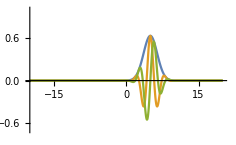
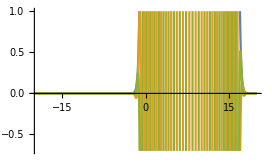
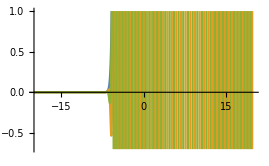
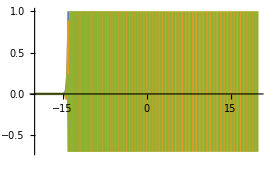
Something really strange seems to happen with  our wave packet--it grows without bound.  That’s a bit alarming! So even though this potential supposedly has real eigenvalues, it seems like energy is not conserved. That’s a bit of a problem. Check out time steps 1, 10, 20 and 50 below. 
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Clear[imagEVectorsRe,imagEVectorsIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=6;
periodicChoice=2;
 schemeChoice=2;
imagEValuesRE=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦1⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
imagEValuesIm=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦2⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
Do[
Evaluate[Symbol["imagEVectors"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>"_"<>eigenState⟦2⟧<>".csv","CSV"];,
{i,2}];
imagEVectors=Sqrt[imagEVectorsRe^2+imagEVectorsIm^2];
];
```

```mathematica
Manipulate[ListPlot[{imagEVectors⟦All,i⟧,imagEVectorsRe⟦All,i⟧,imagEVectorsIm⟦All,i⟧,imagPotential/25},Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,PlotRange->{{-20,20},{-.2,.2}}],{i,1,Length[imagEVectors⟦All,1⟧],1}]
```

These eigenstates look like complex wave packets. Check out 319:

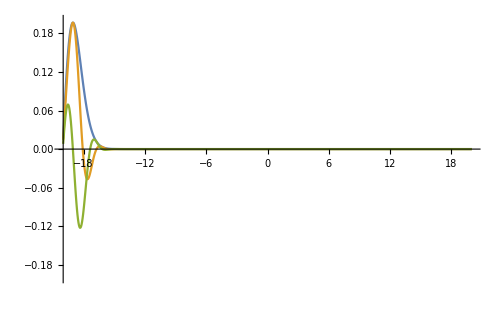

```mathematica
Manipulate[{imagEValuesRE[[i]],imagEValuesIm[[1]]"i"},{i,1,Length[imagEValues],1}]
```

We expect to see real eigenvalues... but we see THE SAME imaginary component for all eigenvalues. That’s odd.

## V=x+ix

```mathematica
Clear[complexCNRe,complexCNIm,complexCN,complexPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=7;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["complexCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
complexPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
complexCN=Sqrt[complexCNRe^2+complexCNIm^2];
];
Manipulate[ListPlot[{complexCN⟦t,All⟧,complexCNRe⟦t,All⟧,complexCNIm⟦t,All⟧,complexPotential},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[complexCNRe⟦All,1⟧],1}]
```

This seems to suffer from the similar problem as the last potential, except first it collapses. See timesteps 1, 10, 20, and 50 below (left to right order).

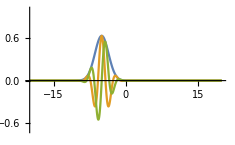
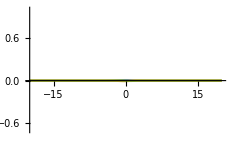
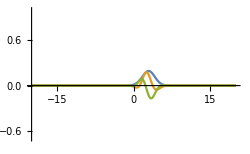
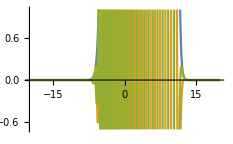

```mathematica
Clear[complexEVectorsRe,complexEVectorsIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=7;
periodicChoice=2;
 schemeChoice=2;
complexEValuesRE=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦1⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
complexEValuesIm=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦2⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
Do[
Evaluate[Symbol["complexEVectors"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>"_"<>eigenState⟦2⟧<>".csv","CSV"];,
{i,2}];
complexEVectors=Sqrt[complexEVectorsRe^2+complexEVectorsIm^2];
];
```

```mathematica
Manipulate[ListPlot[{complexEVectors⟦All,i⟧,complexEVectorsRe⟦All,i⟧,complexEVectorsIm⟦All,i⟧,complexPotential/25},Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,PlotRange->{{-20,20},{-.2,.2}}],{i,1,Length[complexEVectors⟦All,1⟧],1}]
```

These look a lot like the eigenvectors of our last potential. Check out 220, 222, and 226 (left to right)

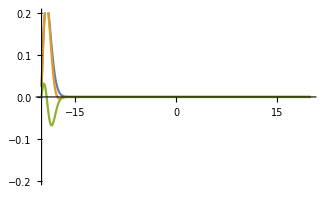
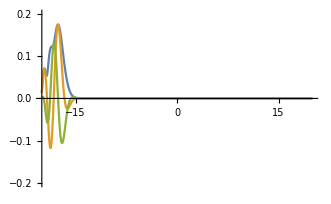
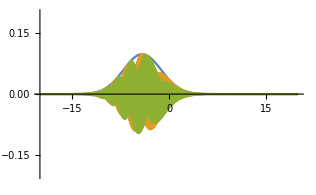

```mathematica
Manipulate[{complexEValuesRE[[i]],complexEValuesIm[[1]]"i"},{i,1,Length[complexEValuesRE],1}]
```

This has suffered the same fascinating fate as the previous potential--we have the same imaginary part of each eigenvalue. So perhaps it’s some quirk of our scheme.

## Conclusion

Broadly, our results using the Crank-Nicolson scheme predict the behavior that we would expect to see for wave packets. . For the square well and harmonic oscilator potentials, the Crank-Nicolson scheme largely preserves the eigenstates over time. For the barrier, the results are qualitatively consistent with analytical results, though they are off significantly when it comes to the exact numbers. This may be due to the vary narrow barrier, which cases more sensitivity to rounding errors (both in our analytical calculation and in the numerical approximations).

Intriguingly, initial wave packets incident on the complex potentials seem to explode. We don’t have a good explanation for this. We also have a baffling constant imaginary term in the eigenvalues for each of these which is puzzling.